# Mathematica as a Tool for Astronomy and Physics

## Lecture 11 Wintersemester 2009/10 Markus Röllig

## Differential Equations

Required Reading

Differential Equations
Differential Equations
Differential Equation Solving with DSolve

The basic command to solve a differential equation symbolically is DSolve. DSolve[eqn,y,x]solves a differential equation for the function y, with independent variable x. The result of a successfully solved differential equation is a list of lists of rules—structurally, like the result of Solve.  DSolve can handle the following types of equations:

Ordinary Differential Equations (ODEs), in which there is a single independent variable t and one or more dependent variables x_i(t). DSolve is equipped with a wide variety of techniques for solving single ODEs as well as systems of ODEs.

Partial Differential Equations (PDEs), in which there are two or more independent variables and one dependent variable. Finding exact symbolic solutions of PDEs is a difficult problem, but DSolve can solve most first-order PDEs and a limited number of the second-order PDEs found in standard reference books.

Differential-Algebraic Equations (DAEs), in which some members of the system are differential equations and the others are purely algebraic, having no derivatives in them. As with PDEs, it is difficult to find exact solutions to DAEs, but DSolve can solve many examples of such systems that occur in applications.

### Symbolic Solution to ODE's

Required Reading

Overview of Ordinary Differential Equations (ODEs)

DSolve[eqn,y[x],x] solve a differential equation for y[x]
DSolve[{eqn_1,eqn_2,…},{y_1[x],y_2[x],…},x] solve a system of differential equations for y_i[x]

One of the simplest differential equations is y'(x)==y(x) .

```mathematica
DSolve[y'[x]==y[x],y[x],x]
```

You can pick out a specific solution by using /. (ReplaceAll).

```mathematica
y[x]/.DSolve[{y'[x]==y[x]}, y[x], x]
```

Integration constants are given as C[n]. If we provide initial conditions we get particular solution. The condition has not to be numeric. Symbolic conditions work as well

```mathematica
DSolve[{y'[x]==y[x],y[0]==a},y[x],x]
```

```mathematica
DSolve[{y'[x]==y[x],y[0]==2},y[x],x]
```

You can also ask DSolve to use a different set of integration constants by using the option GeneratedParameters:

```mathematica
DSolve[{y'[x]==y[x]},y[x],x,GeneratedParameters->Ϡ]
```

One way to visualize differential equations is by plotting the so-called direction field. This is related to the geometrical interpretation of a differential equation ⅆy/ⅆx=f(x,y).Suppose that a solution to this equation is a function ϕ(x), so a solution is the graph of the function ϕ. Therefore, if (x, y) is a point on this graph, the slope of the tangent line is given by f (x, y). A set of short line segments representing the tangent lines can be constructed for a large number of points. This collection of line segments is known as the direction field of the differential equation and provides a great deal of information concerning the behavior of the family of solutions. Mathematica offers the function VectorPlot and VectorPlot3D to visualize the direction field.

VectorPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}]  generates a vector plot of the vector field {v_x,v_y} as a function of x and y. Our example ODE from above has the following direction field:

```mathematica
VectorPlot[{1,y},{x,-3,3},{y,-3,3}]
```

A particular solution to the ODE overlayed to the direction field:

```mathematica
Show[{%,Plot[2Exp[x],{x,-3,3},PlotStyle->{Red,Thick}]}]
```

Another way to visualize the behavior of differential eqautions is by plotting various solutions for different initial conditions

```mathematica
sol= DSolve[ y'[ x]== (x^2-y[x])/(x+y[x]),y,x]
particularSolutions =Table[
Tooltip[y[x]/.sol/.C[1]-> k,k],{k,-10,10}];
Plot[particularSolutions,{x,-4,4}]
```

The differential equation has to be given by using the y'[x] (Derivative) command or D[f,x] (D or ∂ ).

```mathematica
DSolve[y''[x]==x^2,y[x],x]
```

```mathematica
DSolve[D[y[x],{x,2}]==x^2,y[x],x]
```

Here is a more complicated example. Similar to the results of Integrate and Sum, DSolve-results often contain special functions, Root-objects, and RootSum-objects.

```mathematica
DSolve[{y'[x] == y[x]^2 - x}, y[x], x]
```

```mathematica
VectorPlot[{1,y^2-x},{x,-2,2},{y,-2,2}]
```

```mathematica
sol=DSolve[{y'[x] == y[x]^2 - x,y[0]==1}, y, x]
```

```mathematica
Show[{%%,Plot[y[x]/.sol,{x,-2,2},PlotStyle->{Red,Thick}]}]
```

The specification of the functions in the second argument of DSolve is analogous to that for NDSolve; that is, if no argument is specified for the function to be found, DSolve returns a pure function (with the dummy variable typically being the independent variable from the input equations). Here this is demonstrated using the simple differential equation y''(x)=-y(x)

```mathematica
y1=DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
```

```mathematica
y2=DSolve[y'[x]+y[x]==a Sin[x],y,x]
```

SInce the solution is given as a pure function named y without specifying the argument it can be used to replace any instance of y[anyArgument].

```mathematica
{y /. y2, Integrate[(x y[z]) /. y2, z]}
```

y1 can not be used in the same way. y[z] does not match y[x] and so the integrand is not replaced.

```mathematica
{y /. y1, Integrate[(x y[z]) /. y1, z]}
```

Because of the pure function form of the solution, arbitrary derivatives Derivative[n][solution] can also be immediately replaced.

You can use the replacement, e.g. if you want to plot the solution

```mathematica
DSolve[{y''[x]-x y[x]==0,y[0]==1,y[9]==1},y,x]
Plot[y[x]/.%,{x,-10,10}]
```

Often you will encounter special functions on the solution of differential equations

```mathematica
DSolve[{w'[z] == Exp[z^2], w[0] == 0}, w, z]
```

Often DSolve can integrate the differential equation but Solve can not resolve the resulting equation for the dependant variables. The solution is the given in implicit form or using InverseFunction[function].

```mathematica
DSolve[{y'[x] == Log@y[x]} , y, x]
```

Although the initial conditions are usually specified in terms of simple equations like x[0]==x_0, it is also possible to use more complicated equations whose solutions may include several sets of  initial conditions, in which case  DSolve produces several solutions to the differential equation.  The following variation of the shm problem appears contrived, but illustrates the idea.

```mathematica
DSolve[{x''[t]== -Subscript[ω, 0]^2 x[t], (Subscript[ω, 0] x[0]-x'[0])^2==Subscript[v, 0]^2, Subscript[ω, 0] x[0]+x'[0]==0}, x, t]
```

DSolve also solves some boundary-value problems (but it typically does not find all possible solutions). In the following example, these are y_k(x)=csin(kx),kϵ"ℤ". The k=1 solution is returned in the following example.

```mathematica
DSolve[{y''[x]==-y[x],y[0]==0, y[Pi]==0}, y[x], x]
```

DSolve should be able to solve any linear differential equation with constant coefficients, regardless of order, and many linear equations with nonconstant coefficients up to second order.  Many common special functions were originally defined as solutions to differential equations arising in diverse problems in physics, and hence those equations will usually be recognized.

```mathematica
DSolve[y''[x] - x y[x]==0,y[x],x]
```

```mathematica
DSolve[z^2 y''[z]+z y'[z]+(z^2-n^2) y[z]==0,y,z]
```

```mathematica
DSolve[ y''[z]+(1-n/z^2) y[z]==0,y,z]
```

However, many relatively simple differential equations cannot be solved in terms of named functions.

```mathematica
DSolve[ y''[z]+Sin[z] y[z]==0,y,z]
```

```mathematica
DSolve[ y''[z]+(1-n/z^n) y[z]==0,y,z]
```

Also, systems of coupled differential equations can be solved.

```mathematica
DSolve[{y''[x]==2y[x]+z'[x],z'[x]==2y[x]},{y,z},x]
```

```mathematica
DSolve[{y'[x] == z[x] + 3 x, z'[x] ==2 y[x] + 2 z[x]},
       {y[x], z[x]}, x] //Short[#,8]&
```

```mathematica
With[{θ=Pi/3},DSolve[{y'[x]==Cos[θ]y[x]-Sin[θ]z[x]+1,z'[x]==Sin[θ]y[x]+Cos[θ]z[x],y[0]==1,z[0]==1},{y, z},x]]
Plot[Evaluate[{y[x],z[x]}/.First[%]],{x,0,9}]
```

Piecewise forcing functions:

```mathematica
DSolve[{y'[x]+Clip[x]^2y[x]==0,y[0]==0.5},y[x],x]
Plot[y[x]/.%,{x,-2,2}]
```

```mathematica
DSolve[{y'[x]==Piecewise[{{Cos[x]^2,x >2}}, y[x]^2/3],y[0] == 1},y,x]
Plot[y[x]/.%, {x,0,7}]
```

#### Excercise

Solve y' + y tan(x) = sin(2x) given y=2 when x=0 and verify the solution.

Obtain the symbolic solution to a second-order linear differential equation with constant coefficients in the general form a y'' + b y' + c y = 0 and interpret the solution.

Solve (y')^2+ y=a and verify the solution.

Solve y'+ y^2=a and verify the solution.

Plot the direction field of ⅆy/ⅆx=ⅇ^-x-2y together with various solutions of the DE.

Graph the direction field associated with the DE ⅆy/ⅆx=(cos y - y cos x)/(x sin y + sin x -1)together with some of its solutions.

### Symbolic Solution to PDE's

A partial differential equation (PDE) is a relationship between an unknown function u(x_1,x_2,…,x_n) and its derivatives with respect to the variables x_1,x_2,…,x_n.

```mathematica
equation1=(∂u(x,y))/(∂x)+x (∂u(x,y))/(∂y)==sin(x);
```

PDEs occur naturally in applications; they model the rate of change of a physical quantity with respect to both space variables and time variables. At this stage of development, DSolve typically only works with PDEs having two independent variables.

```mathematica
sol=u/.DSolve[equation1, u, {x,y}][[1]]/.C[1][t_]->t
```

Verifying the solution

```mathematica
equation1 /.{u-> sol}
```

Recall that the general solutions to PDEs involve arbitrary functions rather than arbitrary constants. The reason for this can be seen from the following example.

The partial derivative with respect to y does not appear in this example, so an arbitrary function C[1][y] can be added to the solution, since the partial derivative of C[1][y] with respect to x is 0.

```mathematica
DSolve[D[u[x,y],x]==1, u[x,y],{x,y}]
```

The general solution of the 1D wave equation also contains arbitrary functions.

```mathematica
DSolve[D[ϕ[x, t], x, x] == α^2 D[ϕ[x, t], t, t], ϕ[x, t], {x, t}]
```

The transport equation is a good example of a linear first-order homogeneous PDE with constant coefficients.

```mathematica
DSolve[D[u[x,y],x]+D[u[x,y],y]==0,u[x,y],{x,y}]
```

DSolve can find the general solution for a restricted type of homogeneous linear second-order PDEs; namely, equations of the form

a(∂^2 u)/(∂x^2)+b(∂^2 u)/(∂x ∂y)+c(∂^2 u)/(∂y^2)=0.

Here a, b, and c are constants. Thus, DSolve assumes that the equation has constant coefficients and a vanishing non-principal part.

This finds the general solution of the wave equation, a hyperbolic PDE. The constant c in the wave equation represents the speed of light and is set to 1 here for convenience.

```mathematica
WaveEquation=D[u[x,t],{x,2}]-D[u[x,t],{t,2}]==0;
```

```mathematica
DSolve[WaveEquation , u[x,t], {t,x}]
```

Here is the general solution for Laplace’s equation, an elliptic PDE.

```mathematica
DSolve[D[u[x,y],{x,2}]+D[u[x,y],y,y]==0,u,{x,y}]
```

This general solution contains two arbitrary functions, C[1] and C[2]. The arguments of these functions, y+ⅈx and y-ⅈx, indicate that the solution is constant along the imaginary straight line y=-ⅈx+α when C[2]==0 and along y=ⅈx+α when C[1]==0 . These straight lines are called characteristic curves of the PDE. In general, elliptic PDEs have imaginary characteristic curves.

To find a particular solution we replace the constant functions (in our case we take the exponential function:

```mathematica
sol=%[[1]]/.{C[1][t__]->Exp[t],C[2][t__]->Exp[t]}
```

To verify, that this is actually a solution:

```mathematica
D[u[x,y],{x,2}]+D[u[x,y],y,y]==0/.sol
```

As a last example we take a look at the Burger's equation, which is an important example of a quasi-linear PDE. (∂u(x,y))/(∂x)+u(x,y)(∂u(x,y))/(∂y)==0. We will try to find a solution

```mathematica
DSolve[D[u[x,y],x]+u[x,y]D[u[x,y],y]==0,u[x,y],{x,y}]
```

The solution depends on the 2-dimensional function C[1]. We have to provide a function C[1] so that Mathematica can solve the above output for u[x,y]. Let us assume a simple form of C[1]

```mathematica
sol=%/.C[1][a_,b_]->a-2b
```

To verify that (2y)/(1+2x)actually is a solution we insert it into our initial equation:

```mathematica
D[u[x,y],x]+u[x,y]D[u[x,y],y]==0/.sol[[1]]
```

What happened here? Obviously, the solution only replaced one instance of u[x,y]. The differential operators have not been changed. Take a closer look at

```mathematica
D[u[x,y],x]/.u[x,y]->(2 y)/(1+2 x)
```

Nothing happens. To understand why Mathematica does not apply the replacement rules we will use Trace:

```mathematica
D[u[x,y],x]/.u[x,y]->(2 y)/(1+2 x)//Trace
```

Look at the third output element

```mathematica
%[[3]]
```

Mathematica reformulates D[u[x,y],x] to u^(1,0)[x,y] and then tries to replace any instance of u[x,y]. But syntactically there is no u[x,y] left. We have to prevent the reformulation of the differential before doeing the replacement:. This is done with HoldForm:

```mathematica
D[u[x,y],x]
```

```mathematica
HoldForm[D[u[x,y],x]]
```

Finally, we can verify our solution

```mathematica
HoldForm[D[u[x,y],x]+u[x,y]D[u[x,y],y]==0]/.sol[[1]]//ReleaseHold
```

#### Excercises

Show that u(x,y)=y^2-x^2 and u(x,y)=ⅇ^y sin x are solutions to Laplace's equation u_xx+u_yy=0.

Find a solution of: x u_x=u_y.

Find the general solution to the transport equation, 2 (∂y(x,t))/(∂x)+(∂y(x,t))/(∂t)==0.

### Symbolic Solution to Differential-Algebraic Equations (DAEs)

The systems of equations that govern certain phenomena (in electrical circuits, chemical kinetics, etc.) contain a combination of differential equations and algebraic equations. The differential equations are responsible for the dynamical evolution of the system, while the algebraic equations serve to constrain the solutions to certain manifolds.

Here is a simple example of a DAE. The first equation is an ODE for the function x[t], while the second equation constrains the functions x[t] and y[t] to lie in a submanifold (a straight line) in {x,y} space.

```mathematica
dae =  {x'[t] - y[t]==0, x[t] + y[t] == 0};
```

Linear DAE's are defined as systems of equations of the following type.

A.x'(t)+B.x(t)==F

DSolve can find the solutions to all DAEs in which the entries of the matrices A and B are constants. Such DAEs are said to have constant coefficients.

It is important to realize that the initial values for a DAE must be prescribed carefully to guarantee a solution for the problem. This can be seen by considering the following system of equations.

```mathematica
sol = DSolve[dae, {x,y}, t]
```

This verifies the solution.

```mathematica
dae/.sol//Simplify
```

### Symbolic Solution to Difference Equations

Required Reading:

Solving Recurrence Equations

The discrete analog of differential equations are difference (recurrence) equations.  The Mathematica function to solve difference equations is RSolve.

RSolve[eqn,a[n],n] solves a recurrence equation for a[n].

To start with, here is a simple linear difference equations:

```mathematica
RSolve[u[n + 1] == u[n] - u[n - 1], u[n], n]
```

```mathematica
RSolve[Sum[α[k] u[n + k], {k, 0, 4}] == 0, u[n], n]
```

The simplest possible linear difference equation with non-constant coefficients is

```mathematica
RSolve[Γ[n + 1] == n Γ[n], Γ[n], n]
```

When we add an initial condition the result involves the familiar Gamma function

```mathematica
RSolve[{Γ[n+1]==n Γ[n],Γ[1]==1},Γ[n],n]//FullSimplify
```

A third-order constant coefficient equation:

```mathematica
RSolve[a[n+3]==2a[n], a,n]
```

Initial value conditions:

```mathematica
RSolve[{a[n+3]==2a[n],a[0]==1,a[1]==2,a[2]==-1}, a,n]
```

Plot the solution:

```mathematica
ListPlot[Table[a[n]/.First[%],{n,15}],Filling->Axis]
```

Of course, Mathematica can also solve inhomogeneous difference equations. Here is the corresponding inhomogeneous case with a constant right hand side term

```mathematica
RSolve[{Γ[n+1]-n Γ[n]==A,Γ[1]==1},Γ[n],n]//FullSimplify
```

When the right hand side contains a function of n, the solution will contain a summation with automatically generated dummy variables K$n.

```mathematica
RSolve[{Γ[n+1]-n Γ[n]==A[n],Γ[1]==1},Γ[n],n]//FullSimplify
```

Here is another example with an unspecified coefficient on the right hand side

```mathematica
RSolve[{Ψ[n + 1] == α[n] Ψ[n]}, Ψ[n], n]
```

Here is the simplest possible nonlinear difference equation.

```mathematica
RSolve[u[n + 1] == u[n]^2, u[n], n]
```

Linear system with constant coefficients:

```mathematica
RSolve[{y[n+1]+z[n]==3,y[n]+2 z[n+1]==1},{y[n],z[n]}, n]
```

With boundary conditions:

```mathematica
RSolve[{y[n+1]+z[n]==3,y[n]+2 z[n+1]==1,y[0]==5,z[0]==1},{y,z}, n]
```

Plot their solution:

```mathematica
ListPlot[Transpose @ Table[{y[n],z[n]}/.First[%],{n,0,15}],Filling->Axis]
```

This models the amount a[n] at year n when the interest r is paid on the principal p only:

```mathematica
RSolve[{a[n+1]==a[n]+r p,a[0]==p},a[n],n]//Factor
```

Here the interest is paid on the current amount a[n], i.e. compound interest:

```mathematica
RSolve[{a[n+1]==(1+r)a[n],a[0]==p},a[n],n]
```

Here a[n] is the number of ways to tile a n×3 space with 2×1 tiles:

```mathematica
RSolve[{a[n+4]-4a[n+2]+a[n]==0,a[1]==0,a[2]==3,a[3]==0,a[4]==11},a,n]
```

```mathematica
Table[Evaluate[a[n]/.First[%]],{n,2,20,2}]//Simplify
```

Another class of recurrence equations that is solved by RSolve are q-difference equations. Instead of n+k, one has the multiplicative structure q n. Here are two simple examples of such a q-difference equation.

```mathematica
RSolve[a[q n]==2a[n],a[n],n]
```

```mathematica
RSolve[{a[n]==2a[n/q],a[1]==1},a[n],n]
```

```mathematica
RSolve[u[q n] == u[n] - u[n/q], u[n], n]
```

Note, that by replacing the derivatives in a differential equationsby finite differences we find the related difference equation ∂y/∂x->u(n+1)-u(n). Hence, the ODE y'(x)-y(x)=0 translates to u(n+1)-2u(n)=0.

```mathematica
DSolve[ y'[x] -y[x]== 0,y, x]
RSolve[-2 u[n]+u[1+n]==0,u[n],n]
```

Generally, the n^th-order forward, backward, and central differences are respectively given by (h→1):

Δ_h^n[f](x)=∑_(i=0)^n (-1)^i(n
i)f(x+(n-i)h)
∇_h^n [f](x)=∑_(i=0)^n (-1)^i(n
i)f(x-i h)
δ_h^n[f](x)=∑_(i=0)^n (-1)^i(n
i)f(x+(n/2-i)h)

#### Excercises

Solve the recurrence relation a(n+1)-2a(n)=1.

The factorial can be understood as a recurrence relation of the form a(n+1)=n a(n). Use RSolve to find a generla solution

Find the recurrence relation that is related to the differential equation x y''''[x]+5y'''[x]==24.

### Variational Methods

Required Reading:

Variational Methods Package
Variational Methods

The package VariationalMethods`  implements the calculation of variational derivatives of integrals and the associated Euler-Lagrange equation (for an introduction to variational calculations

The basic problem of the calculus of variations is to determine the function u(x) that extremizes a functional F=∫_x_min^x_max f[u(x),u'(x),x]ⅆx. In general, there can be more than one independent variable and the integrand f can depend on several functions and their higher derivatives.

The extremal functions are solutions of the Euler(–Lagrange) equations that are obtained by setting the first variational derivatives of the functional F with respect to each function equal to zero. Since many ordinary and partial differential equations that occur in physics and engineering can be derived as the Euler equations for appropriate functionals, variational methods are of general utility.

This loads the package.

```mathematica
<<VariationalMethods`
```

VariationalD gives the first variational derivatives of a functional F defined by the integrand f. f may depend on several functions u,v,w,…; their derivatives of arbitrary order; and variables x,y,z,… . EulerEquations returns the Euler(–Lagrange) equations given the integrand f. Again f may depend on several functions u,v,w,…; their derivatives of arbitrary order; and variables x,y,z … .

Here is a well-known example.

```mathematica
VariationalD[Sqrt[1 - y'[x]^2], y[x], x]
```

This is the first variational derivative of F=∫_x_min^x_max y(x)√(1+y'(x)^2)ⅆx.

```mathematica
VariationalD[y[x] √(1+y'[x]^2),y[x],x]
```

EulerEquations[f,u[x],x]returns the Euler–Lagrange differential equation obeyed by u[x] derived from the functional f, where f depends on the function u[x] and its derivatives as well as the independent variable x.

A simple pendulum has the Lagrangian 1/2 m r^2 (θ̇)^2+m g r cos(θ):

```mathematica
EulerEquations[1/2 m r^2 θ'[t]^2+m g r Cos[θ[t]],θ[t],t]
```

The solution to the pendulum equation can be expressed using the function JacobiAmplitude:

```mathematica
DSolve[%,θ[t],t]
```

The next input gives the equation of motion for a damped nonlinear 1D oscillator

```mathematica
EulerEquations[Exp[μ t] (x'[t]^2/2 + a/2 x[t]^2 + b/(n + 1) x[t]^n),
               {x[t]}, t]
```

Here are the Newton equations of motion for a 2D anharmonic oscillator.

```mathematica
EulerEquations[m/2(x'[t]^2 + y'[t]^2) + (x[t]^4 + x[t] y[t] + y[t]^4),
               {x[t], y[t]}, t]
```

```mathematica
EulerEquations[f[y[x],x],y[x],x]
EulerEquations[f[y'[x],y[x],x],y[x],x]
```

The Lagrangian for a vibrating string yields the classical wave equation:

```mathematica
EulerEquations[1/2 ρ D[u[x,t],t]^2-1/2 τ D[u[x,t],x]^2,u[x,t],{x,t}]
```

The default coordinate system is set to Cartesian and the coordinates are set to x, y, and z.

```mathematica
SetCoordinates[Cartesian[x, y, z]];
```

```mathematica
EulerEquations[1/2 Grad[phi[x,y,z]].Grad[phi[x,y,z]],phi[x,y,z],{x,y,z}]
```

FirstIntegrals[f,u[x],x],FirstIntegrals[f,{u[x],v[x],…},x] give first integrals when the integrand f is independent of one or more of {u[x],v[x],…}, or independent of x

When there is only one independent variable x, FirstIntegrals gives conserved quantities in the following cases: (1) if f does not depend on a coordinate u explicitly, it is referred to as an ignorable coordinate and the corresponding Euler equation possesses an obvious first integral (a conserved generalized momentum), and (2) if f depends on u,v,… and their first derivatives only and has no explicit x dependence, FirstIntegrals also returns the first integral corresponding to the Hamiltonian.

The Lagrangian for central force motion has an ignorable coordinate ϕ (angular momentum conservation) and is independent of time t (energy conservation). FirstIntegrals yields both the first integral corresponding to coordinate ϕ and the first integral corresponding to the Hamiltonian.

```mathematica
FirstIntegrals[1/2 m (r'[t]^2+r[t]^2 phi'[t]^2)-U[r],{r[t],phi[t]},t]
```

The Lagrangian of a particle in 2 dimensions with a central potential:

```mathematica
ℒ=1/2 m(r'[t]^2+r[t]^2 θ'[t]^2)-V[r[t]];
```

The coordinates with conserved first integrals are the angle θ and the time t, corresponding to conservation of angular momentum and energy:

```mathematica
FirstIntegrals[ℒ,{r[t],θ[t]},t]
```

### Numerical Solution to ODE'S

Required Reading:

Numerical Solution of Differential Equations
Advanced Numerical Differential Equation Solving in Mathematica
Stiffness Detection

In the category of numerical methods, one of  the most important built-in command is NDSolve for solving ordinary (also nonlinear and stiff) systems of differential equations.

NDSolve[eqns,y,{x,x_min,x_max}]finds a numerical solution to the ordinary differential equations eqns for the function y with the independent variable x in the range x_min to x_max.

We start with one of the simplest ODE's: the harmonic oscillator:

```mathematica
dg1={x''[t]==-x[t],x[0]==1,x'[0]==1}
sol1=NDSolve[dg1,x[t],{t,0,10}]
```

NDSolve returns its solution(s) in form of InterpolationFunctions. They can be for further processing just lika any other symbolic solution.

```mathematica
Plot[Evaluate[x[t] /. sol1], {t, 0, 10}]
```

Here is a harmonic oscillator with a nonlinear damping

```mathematica
Module[{η = 10^-1, T = 80},
Plot[Evaluate[x[t] /. (* use constant-period damping *)
        NDSolve[{x''[t] == -(x[t] + η Abs[x[t]] x'[t]/Abs[x'[t]]),
         x[0] == 0, x'[0] == 1}, x, {t, 0, T}][[1]]], {t, 0, T},
     Axes -> False, Frame -> True]]
```

A  differential-algebraic equation.

```mathematica
ndsol = 
NDSolve[{x'[t] == 2 x[t] + 3 z[t], y'[t] == -x[t] + y[t] + Sin[y[t]],
         (* no z derivative *) z[t] == -(x[t]^2 + y[t]^2) + z[t]^3,
         (* no initial z-value *) x[0] == 1, y[0] == -1}, {x, y, z},
        {t, -1, 1}]
```

```mathematica
Plot[Evaluate[{x[t], y[t], z[t]} /. ndsol[[1]]], {t, -1, 1},
     Frame -> True, Axes -> False, PlotRange -> All]
```

NDSolve also solves large systems of differential equations in an acceptable time. Here is a system of 10 second-order differential equations that are coupled nonlinearly with one another. We chose the constants and the exponents randomly.

```mathematica
num = 10;
SeedRandom[1234567];
(diffEqn = Table[x[i]''[t] == Sum[Random[Integer, {-2, 2}] *
                        x[j][t]^Random[Integer, {0, 3}], {j, num}],
                 {i, num}]) // Short[#, 16]&
```

Next, we add initial conditions.

```mathematica
eqn = Join[diffEqn, Table[x[i] [0] == 1, {i, num}],
                    Table[x[i]'[0] == 1, {i, num}]];
```

Here is the solution of the system of differential equations.

```mathematica
Timing[sol = NDSolve[eqn, Table[x[i], {i, num}], {t, 0, 1/2}]]
```

```mathematica
Plot[Evaluate[Table[x[i][t] /. sol, {i, num}], {t, 0, 1/2},
     PlotStyle -> Table[Hue[j/10 0.7], {j, num}], PlotRange -> All]]
```

The following are the Lotka-Volterra Equations, describing predator-prey relations

```mathematica
NDSolve[{y'[t]==y[t](x[t]-1),x'[t]==x[t](2-y[t]),x[0]==1,y[0]==2.7},{x,y},{t,0,10}]
```

```mathematica
Plot[Evaluate[{x[t],y[t]}/.First[%]],{t,0,10}]
```

Here is the corresponding Phase-plane plot

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.First[%%]],{t,0,10}]
```

Next we examine two masses connected by a spring, one mass connected to the origin by spring

```mathematica
spring[xkezd_,ykezd_,xveg_,yveg_]:={
hx=xveg-xkezd;hy=yveg-ykezd;szel=0.2;veghossz=0.3;
hossz=√(hx^2+hy^2);
dh=(hossz-2*veghossz)/30;
{xkezd,ykezd}}~Join~{{xkezd+hx*(dh+veghossz)/hossz,ykezd+hy*(dh+veghossz)/hossz}}~Join~Table[If[OddQ[i],{xkezd+hx*(i*dh+veghossz)/hossz+hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz-hx*szel/hossz},
{xkezd+hx*(i*dh+veghossz)/hossz-hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz+hx*szel/hossz}],{i,2,28}]~Join~{{xkezd+hx*(29*dh+veghossz)/hossz,ykezd+hy*(29*dh+veghossz)/hossz}}~Join~{{xveg,yveg}};
```

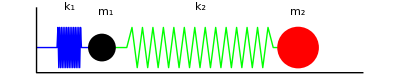

```mathematica
Graphics[{
Green,Line@spring[1,0,4,0],
Blue,Line@spring[0,0,1,0],
Black,PointSize[0.05],Point[Evaluate[{1,0}]],
PointSize[0.075],Red,Point[Evaluate[{4,0}]],
Black,Thick,Line[{{0,0.4},{0,-0.25},{5,-0.25}}],
Text["k_1",{0.5,0.4}],
Text["k_2",{2.5,0.4}],
Text["m_1",{1.05,0.35}],
Text["m_2",{4,0.35}]},
Frame->False]
```

```mathematica
sol=NDSolve[{
x1''[t]==- x1[t]+3(x2[t]-x1[t]),(* Subscript[k, 1]=1,Subscript[m, 1]=1,Subscript[k, 2]=3,Subscript[m, 2]=2 *)
2x2''[t]==-3(x2[t]-x1[t]),
x1[0]==1,
x2[0]==4,
x1'[0]==0,
x2'[0]==0},
{x1,x2},{t,20}]
```

```mathematica
Plot[Evaluate[{x1[t],x2[t]}/.sol[[1]]],{t,0,20}]
```

```mathematica
Animate[
Graphics[{
Green,Line@spring[x1[t],0,x2[t],0],
Blue,Line@spring[0,0,x1[t],0],
Black,PointSize[0.05],Point[Evaluate[{x1[t],0}]],
Red,PointSize[0.075],Point[Evaluate[{x2[t],0}]]
}/.sol[[1]],
PlotRange->{{-5,5},{-0.5,0.5}},Frame->True],{t,0,20,0.01}]
```

Two coupled pendula

```mathematica
sol=NDSolve[{
x1''[t]==-g/l x1[t]-k/m1(x1[t]-x2[t]),x2''[t]==-g/l x2[t]-k/m2(x1[t]-x2[t]),
x1[0]==-5,
x2[0]==5,
x1'[1]==0,x2'[1]==1.2}/.{m1->1,m2->10,k->1,l->2,g->10},{x1,x2},{t,0,300}];
```

```mathematica
Animate[
Graphics[{
Green,Line@spring[x1[t],-2,x2[t],-2],
Blue,Line[{{-5,0},{x1[t],-2}}],Blue,Line[{{5,0},{x2[t],-2}}],
Black,PointSize[0.05],Point[Evaluate[{x1[t],-2}]],
Red,PointSize[0.075],Point[Evaluate[{x2[t],-2}]]
}/.sol[[1]],
PlotRange->{{-27,27},{-2.5,0.5}},Frame->True,AspectRatio->0.6],{t,0,50,0.01},AnimationRate->0.75]
```

Two-armed pendulum: Let us start with the Lagrangian:

```mathematica
T=1/2 m1 l1^2(θ[1]'[t])^2+1/2 m2(l1^2(θ[1]'[t])^2+l2^2(θ[2]'[t])^2+2l1 l2 θ[1]'[t]θ[2]'[t]Cos[θ[1][t]-θ[2][t]]);
V=m1 g(l1+l2-l1 Cos[θ[1][t]])+m2 g(l1+l2-(l1 Cos[θ[1][t]]+l2 Cos[θ[2][t]]));
L=T-V
L=L/.{l1->l,l2->l,m1->m,m2->m} (* let's simplify a little *)
```

ⅆ/ⅆt((∂L)/(∂(θ̇)_1))-(∂L)/(∂θ_1)==0 , ⅆ/ⅆt((∂L)/(∂(θ̇)_2))-(∂L)/(∂θ_2)==0  are the Lagrange equations connected to θ_1 and θ_2.

```mathematica
{eq1=Dt[D[L,θ[1]'[t]],t, Constants -> {m,l,g}]-D[L,θ[1][t]]==0//FullSimplify,
eq2=Dt[D[L,θ[2]'[t]],t, Constants -> {m,l,g}]-D[L,θ[2][t]]==0//FullSimplify};
```

Divide both sides of the equation by l m.

```mathematica
eq1=#/(l m)&/@eq1
eq2=#/(l m)&/@eq2
```

Insert numbers

```mathematica
eq1=eq1/.{g->9.8,l->1};
eq2=eq2/.{g->9.8,l->1};
```

sol solves any given set of initial conditions

```mathematica
sol[a1_?NumberQ,a2_?NumberQ,v1_?NumberQ,v2_?NumberQ]:=NDSolve[{eq1,eq2,θ[1][0]==a1,θ[2][0]==a2,θ[1]'[0]==v1,θ[2]'[0]==v2},{θ[1],θ[2]},{t,1,100},MaxSteps->Infinity]
```

The {x,y] coordinates of the both arms

```mathematica
pos[1][t_]:={Sin[θ[1][t]],-Cos[θ[1][t]]}
pos[2][t_]:={Sin[θ[1][t]]+Sin[θ[2][t]],-Cos[θ[1][t]]-Cos[θ[2][t]]}
```

This function actually draws the animation.

```mathematica
pendel[a1_?NumberQ,a2_?NumberQ,v1_?NumberQ,v2_?NumberQ]:=Animate[Graphics[{Thickness[0.01],Line[{{0,0},pos[1][t],pos[2][t]}],PointSize[0.05],Point[pos[1][t]],Red,Point[pos[2][t]]}/.sol[a1,a2,v1,v2],PlotRange->{{-2,2},{-2.5,1}},Frame->True],{t,1,50,0.002},AnimationRate->0.75]
```

```mathematica
pendel[0,3,0,2]
```

```mathematica
pendel[0,0,1,0]
```

```mathematica
pendel[10,-10,5,-15]
```

NDSolve also solves systems of stiff differential equations.

Again we take a look at the pendulum. Consider a mass m, conneted to the point {0,0,0} by a massless spring. Let us solve the problem in 3 dimensions:

```mathematica
Federpendel[{x0_,y0_,z0_},{vx0_,vy0_,vz0_},m_,l0_,k_,time_]:=Module[{V,T,L,eq1,eq2,eq3,inipos,inivel,sol,g=9.81,x,z,y},
V=1/2 k(√((x[1][t])^2+(y[1][t])^2+(z[1][t])^2)-l0)^2+m g z[1][t];
T=1/2 m((x[1]'[t])^2+(y[1]'[t])^2+(z[1]'[t])^2);
L=T-V;
{eq1=Dt[D[L,x[1]'[t]],t, Constants -> {m,l0,k,g}]-D[L,x[1][t]]==0//FullSimplify,
eq3=Dt[D[L,z[1]'[t]],t, Constants -> {m,l0,k,g}]-D[L,z[1][t]]==0//FullSimplify,
eq2=Dt[D[L,y[1]'[t]],t, Constants -> {m,l0,k,g}]-D[L,y[1][t]]==0//FullSimplify};
inipos={x[1][0]==x0,y[1][0]==y0,z[1][0]==z0};
inivel={x[1]'[0]==vx0,y[1]'[0]==vy0,z[1]'[0]==vz0};
sol=NDSolve[Join[{eq1,eq2,eq3},inipos,inivel],{x[1],y[1],z[1]},{t,0,time}];
Animate[Graphics3D[Evaluate[{Thickness[0.02],Blue,
Line[{{0,0,0},{x[1][t],y[1][t],z[1][t]}}],Red,PointSize[0.1],Sphere[{x[1][t],y[1][t],z[1][t]},0.5]}/.sol],PlotRange->{{-3,3},{-3,3},{3,-5}}],{t,0,time,time/10000.},AnimationRate->0.5]]
```

Now we can easily upgrade our model to two masses with two springs:

```mathematica
Federpendel2[{x10_,y10_,z10_},{x20_,y20_,z20_},{vx10_,vy10_,vz10_},{vx20_,vy20_,vz20_},m1_,m2_,l01_,l02_,k1_,k2_,time_]:=Module[{V,T,L,eq1,eq2,eq3,eq4,eq5,eq6,inipos,inivel,sol,g=9.81,x,z,y},
V=1/2 k1(√((x[1][t])^2+(y[1][t])^2+(z[1][t])^2)-l01)^2+1/2 k2(√((x[1][t]-x[2][t])^2+(y[1][t]-y[2][t])^2+(z[1][t]-z[2][t])^2)-l02)^2+m1 g z[1][t]+m2 g z[2][t];
T=1/2 m1((x[1]'[t])^2+(y[1]'[t])^2+(z[1]'[t])^2)+1/2 m2((x[2]'[t])^2+(y[2]'[t])^2+(z[2]'[t])^2);
L=T-V;
{eq1=Dt[D[L,x[1]'[t]],t, Constants -> {m1,m2,l01,l02,g,k1,k2}]-D[L,x[1][t]]==0//FullSimplify,
eq2=Dt[D[L,x[2]'[t]],t, Constants -> {m1,m2,l01,l02,g,k1,k2}]-D[L,x[2][t]]==0//FullSimplify,
eq3=Dt[D[L,y[1]'[t]],t, Constants -> {m1,m2,l01,l02,g,k1,k2}]-D[L,y[1][t]]==0//FullSimplify,
eq4=Dt[D[L,y[2]'[t]],t, Constants -> {m1,m2,l01,l02,g,k1,k2}]-D[L,y[2][t]]==0//FullSimplify,
eq5=Dt[D[L,z[1]'[t]],t, Constants -> {m1,m2,l01,l02,g,k1,k2}]-D[L,z[1][t]]==0//FullSimplify,
eq6=Dt[D[L,z[2]'[t]],t, Constants -> {m1,m2,l01,l02,g,k1,k2}]-D[L,z[2][t]]==0//FullSimplify};
inipos={x[1][0]==x10,y[1][0]==y10,z[1][0]==z10,x[2][0]==x20,y[2][0]==y20,z[2][0]==z20};
inivel={x[1]'[0]==vx10,y[1]'[0]==vy10,z[1]'[0]==vz10,x[2]'[0]==vx20,y[2]'[0]==vy20,z[2]'[0]==vz20};
sol=NDSolve[Join[{eq1,eq2,eq3,eq4,eq5,eq6},inipos,inivel],{x[1],x[2],y[1],y[2],z[1],z[2]},{t,0,time}];
Animate[Graphics3D[Evaluate[{Thickness[0.03],Blue,
Tube[{{0,0,0},{x[1][t],y[1][t],z[1][t]},{x[2][t],y[2][t],z[2][t]}},0.3],Red,PointSize[0.1],Sphere[{x[1][t],y[1][t],z[1][t]},0.6],Orange,Sphere[{x[2][t],y[2][t],z[2][t]},0.6]}/.sol],PlotRange->{{-4,4},{-4,4},{3,-8}}],{t,0,time,time/10000.},AnimationRate->0.5]]
```

```mathematica
Federpendel2[{0,0,-2},{0,0,-4},{1,0,0},{0,2,0},10,10,1,1,100,100,100]
```

Here is a third version with one spring and a stiff arm, in 2D.

-Graphics-

Kinetic and Potential energy look like:

-Graphics-

```mathematica
Clear[Federpendel3];
Federpendel3[{x10_,y10_,z10_},{vx10_,vy10_,vz10_},m1_,m2_,l01_,l02_,k1_,time_]:=Module[{V,T,L,eq1,eq2,eq3,eq4,eq5,eq6,inipos,inivel,sol,g=9.81,q0,q1,q2},
V=1/2 k1(√(q0[t]^2+q1[t]^2)-l01)^2+m1 g q1[t]+m2 g q1[t]-m2 g l02 Cos[q2[t]];
T=1/2(m1+m2)(q0'[t]^2+q1'[t]^2)+1/2 m2 l02^2 q2'[t]^2+m2 q2'[t] l02(q0'[t]Cos[q2[t]]+q1'[t]Sin[q2[t]]);
L=T-V;
{eq1=Dt[D[L,q0'[t]],t, Constants -> {m1,m2,l01,l02,g,k1}]-D[L,q0[t]]==0//FullSimplify,
eq2=Dt[D[L,q1'[t]],t, Constants -> {m1,m2,l01,l02,g,k1}]-D[L,q1[t]]==0//FullSimplify,
eq3=Dt[D[L,q2'[t]],t, Constants -> {m1,m2,l01,l02,g,k1}]-D[L,q2[t]]==0//FullSimplify};
inipos={q0[0]==x10,q1[0]==y10,q2[0]==z10};
inivel={q0'[0]==vx10,q1'[0]==vy10,q2'[0]==vz10};
sol=NDSolve[Join[{eq1,eq2,eq3},inipos,inivel],{q0,q1,q2},{t,0,time}];
Animate[Graphics[Evaluate[{
Blue,
Line@spring[0,0,q0[t],q1[t]],Thickness[0.01],Line[{{q0[t],q1[t]},{q0[t]+l02 Sin[q2[t]],q1[t]-l02 Cos[q2[t]]}}],Red,Disk[{q0[t],q1[t]},0.6],Orange,Disk[{q0[t]+l02 Sin[q2[t]],q1[t]-l02 Cos[q2[t]]},0.6]}/.sol],PlotRange->{{-4,4},{0,-8}}],{t,0,time,time/10000.},AnimationRate->0.5]]
```

```mathematica
Federpendel3[{0,-2,1},{0,0,0},10,10,1,3,100,100]
```

The van der Pol oscillator is a non-conservative oscillator with nonlinear damping and is an example of a stiff system of ordinary differential equations:

```mathematica
vanDerPolSys={y[1]'[t]==y[2][t],ϵ y[2]'[t]==-y[1][t]+(1-(y[1][t])^2)y[2][t],y[1][0]==2,y[2][0]==0}/.ϵ->3/1000;
```

Solution without any Options specified

```mathematica
sol1=NDSolve[vanDerPolSys,{y[1],y[2]},{t,0,10}]
```

Using Extrapolation method fails

```mathematica
sol2=NDSolve[vanDerPolSys,{y[1],y[2]},{t,0,10}, Method -> "Extrapolation"]
```

Solve the system using a method that switches when stiffness occurs.

```mathematica
sol3=NDSolve[vanDerPolSys,{y[1],y[2]},{t,0,10}, Method -> {"StiffnessSwitching","NonstiffTest"->False}]
```

```mathematica
{Plot[Evaluate[{y[1][t],y[2][t]}/.sol1], {t, 0, 10}, 
PlotStyle -> {{Red}, {Blue}}, Axes -> False, Frame -> True],
Plot[Evaluate[{y[1][t],y[2][t]}/.sol2], {t, 0, 10}, 
PlotStyle -> {{Red}, {Blue}}, Axes -> False, Frame -> True],
Plot[Evaluate[{y[1][t],y[2][t]}/.sol3], {t, 0, 10}, 
PlotStyle -> {{Red}, {Blue}}, Axes -> False, Frame -> True]}
```

```mathematica
Plot[Evaluate[{x[t], y[t]} /.
         NDSolve[{x''[t] == -300 x[t] + 1/(1 + y[t]),
                  y'[t] == -t y[t] + x[t] y[t],
                  x[0] == 1, x'[0] == 0, y[0] == 1},
                  {x[t], y[t]}, {t, 0, 4}]],
     {t, 0, 4}, PlotRange -> All]
```

NDSolve accepts a number of options to control the solution process.

```mathematica
Options[NDSolve]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,EvaluationMonitor→None,InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→10000,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,SolveDelayed→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

Some of the options can also take sub-option settings

```mathematica
Options[NDSolve`ExplicitRungeKutta]
```

{Coefficients→EmbeddedExplicitRungeKuttaCoefficients,DifferenceOrder→Automatic,EmbeddedDifferenceOrder→Automatic,StepSizeControlParameters→Automatic,StepSizeRatioBounds→{1/8,4},StepSizeSafetyFactors→Automatic,StiffnessTest→Automatic}

#### Excercise

Find a numeric solution to the following pendulum plus visualization:

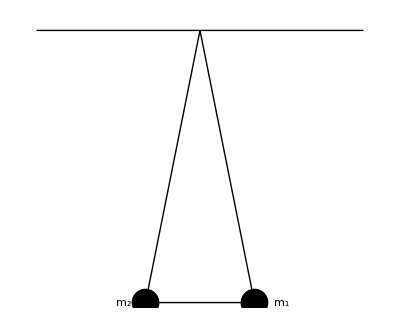

```mathematica
Graphics[{
Black,PointSize[0.05],Point[{1,-5}],
PointSize[0.05],Point[{-1,-5}],
Line[{{0,0},{1,-5},{-1,-5},{0,0}}],
Text["m_1",{1.5,-5}],
Text["m_2",{-1.4,-5}],
Black,Thick,Line[{{-3,0},{3,0}}]},
Frame->False]
```

Find a numeric solution to the following pendulum plus visualization:

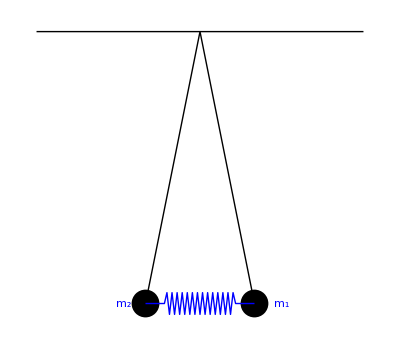

```mathematica
Graphics[{
Black,PointSize[0.05],Point[{1,-5}],
PointSize[0.05],Point[{-1,-5}],
Line[{{-1,-5},{0,0},{1,-5}}],
Blue,Line@spring[-1,-5,1,-5],
Text["m_1",{1.5,-5}],
Text["m_2",{-1.4,-5}],
Black,Thick,Line[{{-3,0},{3,0}}]},
Frame->False]
```

Find a numeric solution of the following system of masses connected with springs and visualize the solution.

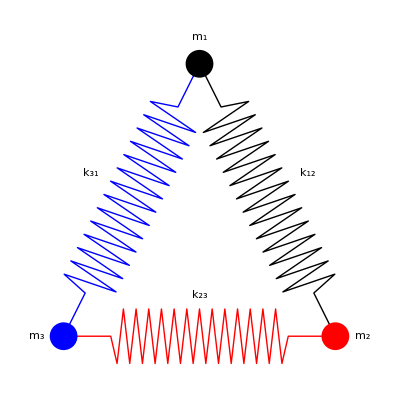

```mathematica
Graphics[{
Black,Line@spring[0,2,1,0],
Red,Line@spring[1,0,-1,0],
Blue,Line@spring[-1,0,0,2],
Black,PointSize[0.05],Point[{0,2}],
PointSize[0.05],Red,Point[{1,0}],
Blue,PointSize[0.05],Point[{-1,0}],
Black,
Text["k_12",{0.8,1.2}],
Text["k_23",{0,.3}],
Text["k_31",{-0.8,1.2}],
Text["m_1",{0,2.2}],
Text["m_2",{1.2,0}],
Text["m_3",{-1.2,0}]},
Frame->False]
```

Generalize the above problem to any given n-gon and write a program to solve it and show the solution.

### Numerical Solution to PDE'S

Required Reading:

Numerical Solution of Partial Differential Equations

NDSolve currently uses the numerical method of lines (1+1 dimensions) to compute solutions to partial differential equations. The numerical method of lines is a technique for solving partial differential equations by discretizing in all but one dimension, and then integrating the semi-discrete problem as a system of ODEs or DAEs. The method is restricted to problems that can be posed with an initial condition
in at least one independent variable. For example, the method cannot solve elliptic PDEs such
as Laplace's equation because these require boundary values. For the problems it does solve,
the method of lines is quite general, handling systems of PDEs or nonlinearity well, and often
quite fast.

This solves the heat equation in 1 dimension. A Simple model for soil temperature at depth x with periodic heating at the surface:

```mathematica
NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}]
Plot3D[Evaluate[u[t,x]/.%],{x,0,5},{t,0,10},PlotRange->All,AxesLabel->Automatic,ColorFunction->Function[{x,y,z},Hue[.65(1-z)]]]
```

Simple wave evolution with periodic boundary conditions, The wave

```mathematica
s=NDSolve[{D[u[t,x], t,t]==D[u[t,x], x,x],u[0,x]==ⅇ^(-x^2),Derivative[1,0][u][0,x]==0,u[t,-10]==u[t,10]},u,{t,0,40},{x,-10,10}]
{DensityPlot[Evaluate[First[u[t,x]/.s]],{t,0,40},{x,-10,10},PlotPoints->30,FrameLabel->Automatic],Plot3D[Evaluate[First[u[t,x]/.s]],{t,0,40},{x,-10,10},PlotPoints->30,AxesLabel->Automatic]}
```

This finds a numerical solution to a generalization of the nonlinear sine-Gordon equation to two
spatial dimensions with periodic boundary conditions.

```mathematica
NDSolve[{D[u[t,x,y],t,t] ==
D[u[t,x,y],x,x]+D[u[t,x,y],y,y]-Sin[u[t,x,y]],u[0,x,y]== Exp[-(x^2+y^2)],Derivative[1,0,0][u][0,x,y]==0,u[t,-5,y] == u[t,5,y] == 0,u[t,x,-5]== u[t,x,5] == 0},u,{t,0,3},{x,-5,5},{y,-5,5}]
```

```mathematica
Plot3D[First[u[3,x,y]/.%],{x,-5,5},{y,-5,5}]
```

#### Excercise

Consider the 2-dim heat equation u^(0,0,1)(x,y,t)==u^(0,2,0)(x,y,t)+u^(2,0,0)(x,y,t). Solve it numerically for -1≤x≤1 and -1≤y≤1and assume the following boundary conditions T->0 at the esges. The initial temperature condition at  t=0 is  Piecewise[{{1, 1/4<x^2+y^2<1/2}, {0, True}}] (use: Piecewise[{{1, 1/4 < x^2 + y^2 < 1/2}}]). Visualize the temperature conditions for different times t.

```mathematica
Plot3D[Piecewise[{{1,1/4<x^2+y^2<1/1.5}}],{x,-1,1},{y,-1,1},PlotRange->All]
```